```mathematica
Clear["Global`*"]
Needs["ToMatlab`"]
```

Needs::nocont: Context ToMatlab` was not created when Needs was evaluated.

```mathematica
dmrnadt[d_, R_, kd_, n_] = R * (  (d/kd)^n/(1+(d/kd)^n) )
```

((d/kd)^n R)/(1+(d/kd)^n)

```mathematica
Manipulate[Plot[dmrnadt[d, R, kd], {d, 1, 3000}], {R, 1, 100}, {kd, 1, 3000}]
```

```mathematica
(*dmRNAdtDist[d_, L_, R_, kd_, n_, v_] = TruncatedDistribution[{0, ∞},NormalDistribution[dmrnadt[d, R, kd, n],v*dmrnadt[d, R, kd, n]]]*)
```

```mathematica
dmRNAdtDist[d_, L_, R_, kd_, n_, v_] = TruncatedDistribution[{0, ∞},LogNormalDistribution[Log[dmrnadt[d, R, kd, n]]-(0.5*v^2),v]]
```

LogNormalDistribution[-0.5 v^2+Log[((d/kd)^n R)/(1+(d/kd)^n)],v]

```mathematica
dmRNAdtObs[d_, L_, R_, kd_, n_, v_] = FullSimplify[Expectation[m\[Conditioned]m>L,m\[Distributed]dmRNAdtDist[d, L, R, kd, n, v]]]
```

Piecewise[{{((d/kd)^n R)/(1.+(d/kd)^n), L≤0}, {((d/kd)^n R (1.+Erf[(0.353553 (v^2-2. Log[L]+2. Log[R-(1. R)/(1.+(d/kd)^n)]))/v]))/((1.+(d/kd)^n) Erfc[(0.353553 (v^2+2. Log[L]-2. Log[R-(1. R)/(1.+(d/kd)^n)]))/v]), True}}]

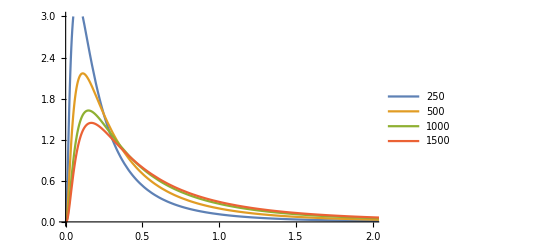

```mathematica
Plot[Table[PDF[dmRNAdtDist[d, 0, 1, 500, 1, 1],x],{d,{250, 500, 1000, 1500}}]//Evaluate,{x,0, 10}, PlotLegends-> {250, 500, 1000, 1500}, PlotRange->{{0,2},{0, 3}}]
```

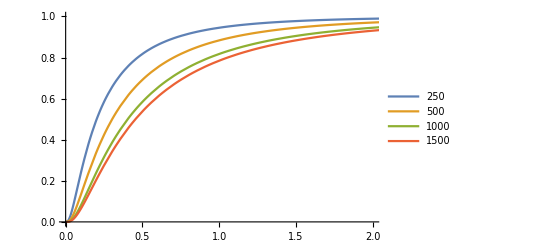

```mathematica
Plot[Table[CDF[dmRNAdtDist[d, 0, 1, 500, 1, 1],x],{d,{250, 500, 1000, 1500}}]//Evaluate,{x,0, 10}, PlotLegends-> {250, 500, 1000, 1500}, PlotRange->{{0,2},{0, 1}}]
```

```mathematica
(*pactive[d_, L_, R_, kd_, n_, v_] = 1  - CDF[dmRNAdtDist[d, L, R, kd, n, v],L]*)
pactive2[d_, L_, R_, kd_, n_, v_] = Probability[m>L,m\[Distributed]dmRNAdtDist[d, L, R, kd, n, v]]
```

Piecewise[{{1/2 Erfc[-(-0.5 v^2-Log[L]+Log[((d/kd)^n R)/(1+(d/kd)^n)])/(√2 v)], L>0}, {1, True}}]

```mathematica
g2[L_, R_, kd_, n_, v_] := Plot[dmRNAdtObs[d, L, R, kd, n, v], {d, 1, 3000}, PlotStyle->Blue, PlotLegends->{"dmRNA/dt observed"}];
g3 [R_, kd_, n_] := Plot[dmrnadt[d, R, kd, n], {d, 1, 3000}, PlotStyle->Red, PlotLegends->{"dmRNA/dt true"}];
g4[L_, R_, kd_, n_, v_] := Plot[pactive2[d,L, R, kd, n, v], {d, 1, 3000}, PlotStyle->Green, PlotLegends->{"fraction active 2"}, PlotRange->{{0 ,3000}, {0, 1}}];
Manipulate[Show[g2[L, R,kd, n,v], g3[R,kd, n], g4[L, R, kd, n, v]], {R, 1, 1}, {kd, 500, 3000}, {L, 0, 1}, {n, 1, 6}, {v, .01, 10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

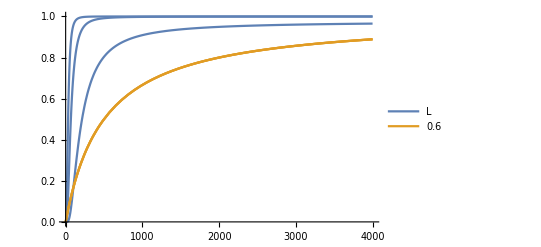
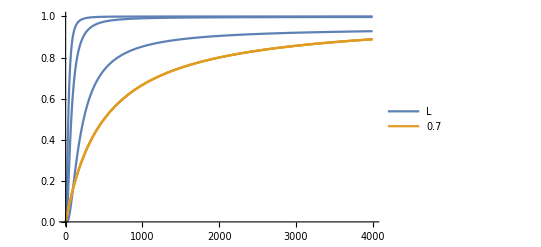
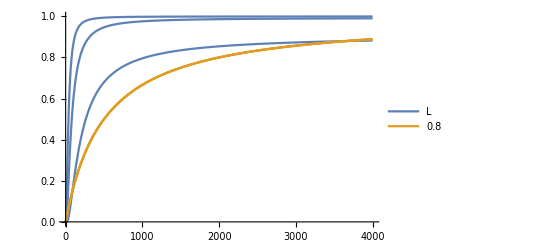

```mathematica
Table[Plot[{Table[{pactive2[d,L, R, kd, n, v]} /. {R->1, kd->500, n->1},{L,{.05, .1, .25}}], Table[{dmrnadt[d, R, kd, n]} /. {R->1, kd->500, n->1},{L,{.05, .1, .25}}]}, {d,0, 4000}, Evaluated->True, PlotLegends->{L,v}], {v,{.6, .7, .8}}]
```

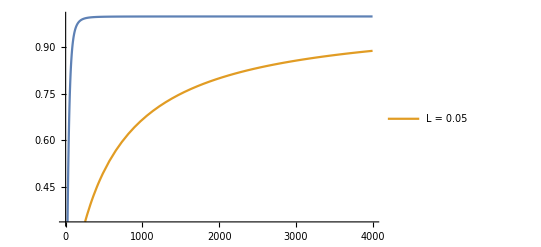
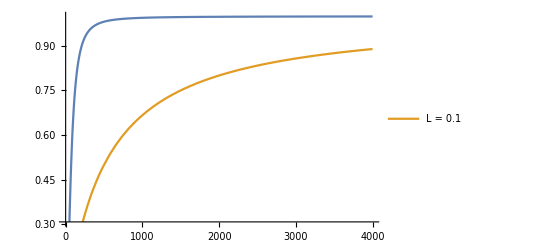
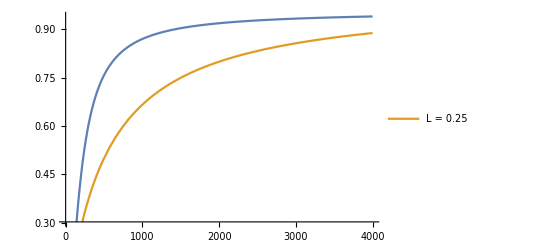

```mathematica
Table[Plot[{pactive2[d,L, R, kd, n, v] , dmrnadt[d, R, kd, n]} /. {R->1, kd->500, n->1, v->.67}, {d,0, 4000}, Evaluated->True, PlotLegends->{"L = "<>ToString[L]}], {L,{.05, .1, .25}}]
```

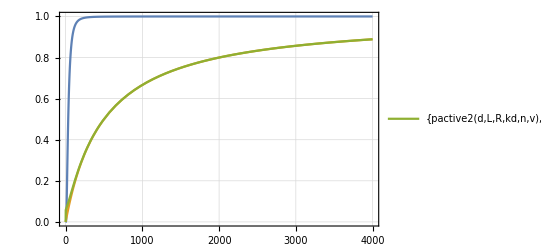
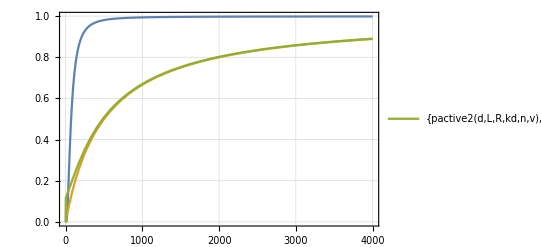
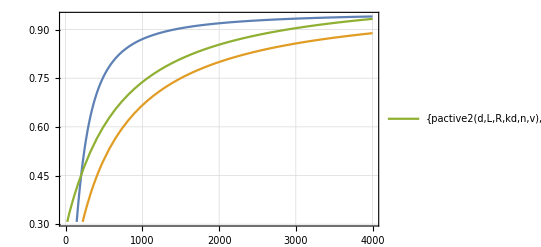

```mathematica
Table[Plot[{pactive2[d,L, R, kd, n, v] , dmrnadt[d, R, kd, n], dmRNAdtObs[d, L, R, kd, n, v]} /. {R->1, kd->500, n->1, v->.67}, {d,0, 4000},  Evaluated->True, PlotTheme->"Detailed"], {L,{.05, .1, .25}}]
```

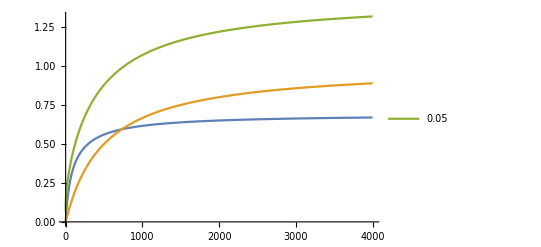
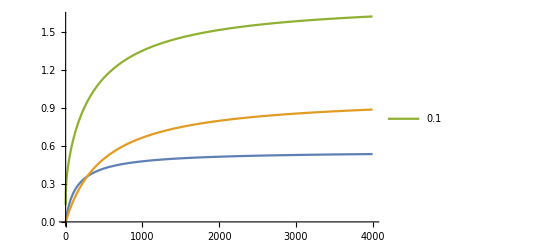
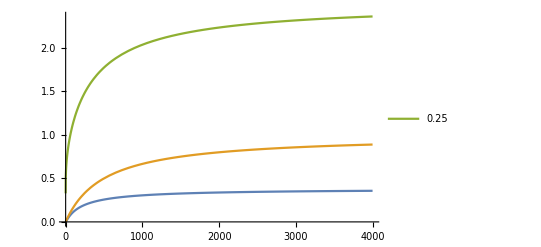

```mathematica
Table[Plot[{pactive2[d,L, R, kd, n, v] , dmrnadt[d, R, kd, n], dmRNAdtObs[d, L, R, kd, n, v]} /. {R->1, kd->500, n->1, v->2}, {d,0, 4000},  Evaluated->True, PlotLegends->{L, L, L}], {L,{.05, .1, .25}}]
```

```mathematica
Table[Plot[{pactive2[d,L, R, kd, n, v], dmrnadt[d, R, kd, n], dmRNAdtObs[d, L, R, kd, n, v]} /. {R->1, kd->500, n->1, v->2}, {d,0, 4000}, PlotLegends->{L},  Evaluated->True], {L,{.05, .1, .25}}]
```

{-Graphics-,-Graphics-,-Graphics-}